# Pendulum. Starter code.

## Small amplitude

```mathematica
SetDirectory[NotebookDirectory[]];
L=0.5;
g = -9.81;
T = 2*Pi*Sqrt[L/Abs[g]]
```

1.4185

## Use differential equation (any amplitude)

0.025

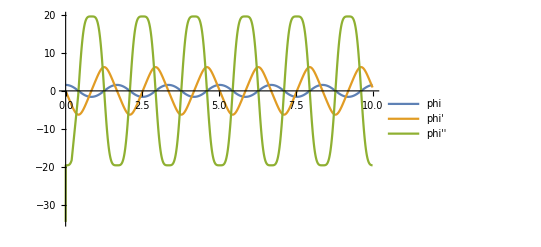

pendulum_p1.eps

```mathematica
m = 0.1;

Subscript[F, t][phi_]:=-m Abs[g]Sin[phi]
MomInertia = m * L^2
s=NDSolve[{phi''[t]==(Subscript[F, t][phi[t]]*L)/MomInertia,phi[0]==Pi/2, phi'[0]==0},phi,{t,0,10}];

p1 = Plot[{Evaluate[phi[t]/.s], Evaluate[phi'[t]/.s], Evaluate[phi''[t]/.s]}
,{t,0,10},PlotRange->All, PlotLegends->{"phi", "phi'", "phi''"}]
Export["pendulum_p1.eps", p1]
```

# Pendulum. Animation. Period.

### Animation

```mathematica
x[t_]:=L*Sin[phi[t]]
y[t_]:=-L*Cos[phi[t]]


MaxTime =2; 

AnF := Animate[
Graphics[
{Red, PointSize -> Large, Point[{x[t], y[t]}/.sol], 
Green, Thick,Line[{{0,0},{x[t], y[t]}}/.sol]},
PlotRange->{{-1.1*L,1.1*L},{-1.1*L,0}},Axes->True,Ticks->False
],
{t, 0, MaxTime, MaxTime/100}, AnimationRunning->False
]

AnF/.sol->s
```

### Compare period at different amplitudes

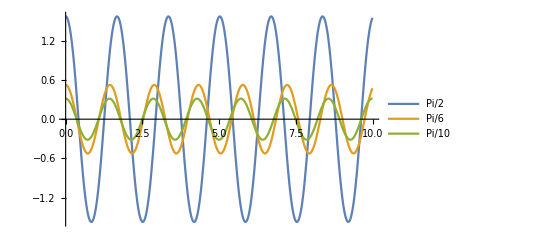

pendulum_p2.eps

```mathematica
s2=NDSolve[{phi''[t]==(Subscript[F, t][phi[t]]*L)/MomInertia,phi[0]==Pi/2, phi'[0]==0},phi,{t,0,10}];
s6=NDSolve[{phi''[t]==(Subscript[F, t][phi[t]]*L)/MomInertia,phi[0]==Pi/6, phi'[0]==0},phi,{t,0,10}];
s10=NDSolve[{phi''[t]==(Subscript[F, t][phi[t]]*L)/MomInertia,phi[0]==Pi/10, phi'[0]==0},phi,{t,0,10}];

p2 = Plot[{Evaluate[phi[t]/.s2], Evaluate[phi[t]/.s6], Evaluate[phi[t]/.s10]}
,{t,0,10},PlotRange->All, PlotLegends->{"Pi/2", "Pi/6", "Pi/10"}]
Export["pendulum_p2.eps", p2]
```

```mathematica
AnF/.sol->s10
```